# Hana Broadband Measurements

## Public measurements of OTWC broadband performance

by Chase.Turner@TFarms.com

For discussion purposes only.  Use of this report requires specific permission of Chase.Turner@TFarms.com

## Terminology

## atlas.ripe.net - Documentation

RIPE Atlas buit-in measurements : https://atlas.ripe.net/docs/built-in
RIPE Atlas : https://atlas.ripe.net/docs

#### Conversion of Unix Machine Timestamp to HST

```mathematica
ClearAll[unixTimeToHST];
(* Hawaiian Timezone is -10 from GMT *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10.0];
(* TEST *)
unixTimeToHST[1330434000]
```

{2012,2,28,10,0,0.}

#### Extract Hour from Date

```mathematica
Clear[hh];hh::useage="Extract the hour from either a {timestamp}, or {{timestamp}, datavalue} dataum";
hh[aDate_List]:= aDate[[4]];
hh[{aTimestamp_List,dataValue_}]:= hh[aTimestamp];
(* TEST *)
hh[{unixTimeToHST[1330434000],"TEST"}]
```

10

## atlas.ripe.net - BuiltIn measurements

### Where to find local data

```mathematica
builtInPathRoot=FileNameJoin[{NotebookDirectory[],"Data","builtIn"}];
```

### Utilities to fetch BuiltIn measurements

#### builtInQuery - convienience function to construct the URL to pull data

```mathematica
Clear[builtInQuery];
```

```mathematica
builtInQuery[probeID_,measurementID_,resolution_,startTime_,endTime_]:= URLBuild[{"https://stat.ripe.net","/data/atlas-ping-measurements/data.json"},
{"probe_id"->probeID, 
"measurement_id"->measurementID,
"starttime"->startTime,
"endtime"->endTime,
"resolution"->resolution (* 0, 1h, 1d, 1w *),
"format"->"json",
"display_mode"->"condensed"}];

(* The following defaults to an early start date and current date *)
builtInQuery[probeID_,measurementID_,resolution_]:= builtInQuery[probeID,measurementID,resolution,"2012-01-01T00:00:00",DateString["ISODateTime"]];

(* FIXME - currently defaulting to 1h; replace with 0 to get it all? *)
builtInQuery[probeID_,measurementID_]:= builtInQuery[probeID,measurementID,"1h"];
```

#### Future API to invoke rather than the above

The following alternate API call is desireable as there is no need to specify the start and stop times.  But calls to this function result in a 404 error.  Manually copying and pasting to a web browser already logged into atlas does work.

Next step is to consult with Atlas to ask them to allow me to generate a key to fetch this information.  NOTE: I did experiment with a variety of private API keys to no avail.

```mathematica
URLBuild[{"https://atlas.ripe.net","/api/v1/measurement/1/result/"},
{"start"->"1330387200",
"stop"->"1441411199",
"probe_id"->"1178",
"key"->"xxxxxxxx-xxxx-xxxx-xxxx-xxxxxxxxxxxx", 
"format"->"json",
"filename"-> "RIPE-Atlas-measurement-1-probe-1178.json"}];
```

#### builtInFilename - convienience function to follow the ATLAS naming convention for measurements

```mathematica
Clear[builtInFilename];
builtInFilename[probeID_,measurementID_]:= "RIPE-Atlas-measurement-"<>ToString[measurementID]<>"-probe-"<>ToString[probeID]<>".json"
```

#### fetchBuiltin - convienience function to fetch and store ATLAS datums. Returns the file path to the cached data file

```mathematica
Clear[builtInFilePath];
```

```mathematica
builtInFilePath[probeID_,measurementID_]:=
Block[
{fileName = builtInFilename[probeID,measurementID],
filePath},

(* Path to find or place the data pulled *)
filePath=FileNameJoin[{builtInPathRoot, fileName}];

(* Return local file or pull and return *)
If[FileExistsQ[filePath],
filePath,
Export[filePath,Import[builtInQuery[probeID,measurementID],"JSON"],"JSON"];filePath]
];

builtInFilePath[probeID_]:=builtInFilePath[probeID,#]&/@{1,2}
```

#### rttDatum - convienience function to fetch a slice of rttDatum of interest.

NOTE : rttDatum is cached and so, if you want to ensure it is re-set, issue the Clear[rttDatum] to force the reload.

```mathematica
Clear[rttDatum];
```

```mathematica
rttDatum[probeID_,hop_,rttMeasurementType_String]:=rttDatum[probeID,hop,rttMeasurementType]=Block[
{
rttMeasurements =( "measurements"/.( "data"/.Import[builtInFilePath[probeID,hop]] )),
rttSlice
},
(* Traverse the JASON structure to reach the slices of interest *)
rttSlice={unixTimeToHST["timestamp"],rttMeasurementType}/.rttMeasurements;
rttSlice
];
```

#### rttDatumForHours - specialization to slice out datums that match a certain hour of the day.

NOTE : rttDatumForHours is cached and so, if you want to ensure it is re-set, issue the Clear[rttDatumForHours] to force the reload.

```mathematica
Clear[rttDatumForHours];
```

```mathematica
rttDatumForHours[probeID_,hop_,rttMeasurementType_String, hours_]:=rttDatumForHours[probeID,hop,rttMeasurementType,hours]=Block[
{
rttDatums = rttDatum[probeID,hop,rttMeasurementType],
hhPattern
},

(* construct DateList patterns to match *)
hhPattern=If[Length[hours]==1, hours, Alternatives[hours]];

(* RETURNING *)
Cases[rttDatums,{{yy_,mm_,dd_,hhPattern,min_,sec_},__}]
];
```

## Hawaii Based Probes

### Probes Of Interest

```mathematica
Clear[probes];
probes::usage="List of probes in Hawaii";
(* Pull 1st and 2nd hop builtIn metrics *)
probes={1178,1165,16065,15111,22773,14720,02289,12735,10546,18657};
(* FIXME - why is Mike's HawaiiTel 16090 returning odd errors? *) 
If[False,AppendTo[{16090},probes], probes];
(* Set to true to add in probes from mainland *)
If[False,AppendTo[{14606},probes], probes];
(* Pull in BuiltIn measurements *)
Parallelize[builtInFilePath[#]& /@probes];
```

### Display and Legends

#### City where probe is located

```mathematica
ClearAll[cProbe];
Block[{},
cProbe::usage="City of the probe";
cProbe[01165]="Maui:Hana";
cProbe[01178]="Maui:Hana";
cProbe[16065]="Maui:Hana";
cProbe[15111]="Maui:Kahului";
cProbe[16090]="Maui:Wailuku";
cProbe[02289]="BI:Hawi";
cProbe[12735]="BI:Kailua-Kona";
cProbe[10546]="BI:Hilo";
cProbe[14720]="Ohau:Kaneohe";
cProbe[18657]="Kauai:Kapaa";
cProbe[22773]="Maui:Kahua";
cProbe[probeID_]:=MessageDialog["FIXME - please cProbe name for probe " <> ToString[probeID]]

];
(* TEST *)
cProbe/@ probes
```

{Maui:Hana,Maui:Hana,Maui:Hana,Maui:Kahului,Maui:Kahua,Ohau:Kaneohe,BI:Hawi,BI:Kailua-Kona,BI:Hilo,Kauai:Kapaa}

#### Whose Probe

```mathematica
ClearAll[wProbe];
Block[{},
wProbe::usage="City of the probe";
wProbe[01165]="Gaylord";
wProbe[01178]="Chase";
wProbe[16065]="BillS";
wProbe[15111]="Harry";
wProbe[16090]="MikeS-HawaiiTel";
wProbe[22773]="MikeS";
wProbe[probeID_]:= cProbe[probeID];
];
(* TEST *)
wProbe/@ probes
```

{Chase,Gaylord,BillS,Harry,MikeS,Ohau:Kaneohe,BI:Hawi,BI:Kailua-Kona,BI:Hilo,Kauai:Kapaa}

#### Color Scheme for probes

```mathematica
ClearAll[colorOf];
Block[{},
colorOf[1165]=Blue;
colorOf[1178]=Red;
colorOf[16065]=Yellow;
colorOf[16090]=Purple;
colorOf[15111]=LightPurple;
colorOf[2289]=Gray;
colorOf[12735]=Orange;
colorOf[10546]=Pink;
colorOf[14720]=LightBrown;
colorOf[18657]=Brown;
colorOf[22773]=LightBrown;
colorOf[probeID_] := MessageDialog["FIXME - please specify color of probe " <> ToString[probeID]];
];
```

#### PlotStyle for probe

```mathematica
ClearAll[plotStyleOf];
plotStyleOf[aProbe_Integer, pSize_, pOpacity_]:=colorOf[aProbe];
(* TEST *)
plotStyleOf[#,.001,0.5]&/@ probes
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0.94, 0.88, 0.94],RGBColor[0.94, 0.91, 0.88],RGBColor[0.94, 0.91, 0.88],GrayLevel[0.5],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.6, 0.4, 0.2]}

#### Pretty Print for Probe

```mathematica
ClearAll[pPrint];
pPrint[probe_Integer]:= Style[" p"<>ToString[probe] <> "_"<>cProbe[probe]<>" ",FontColor->colorOf[probe], Plain,"Text"];

pPrint[probes_List]:= Row[pPrint/@ probes];
(* TEST *)
pPrint/@ probes
```

{ p1178_Maui:Hana , p1165_Maui:Hana , p16065_Maui:Hana , p15111_Maui:Kahului , p22773_Maui:Kahua , p14720_Ohau:Kaneohe , p2289_BI:Hawi , p12735_BI:Kailua-Kona , p10546_BI:Hilo , p18657_Kauai:Kapaa }

## Visualization of Round Trip Time (RTT) of the “Second outbound Hop” to OTWC equipment on Oahu

The “Second outbound Hop” is a measurement of OTWC network infrastructure response times.  Each measurement is an average of 3 tests.   In one year, each atlas.ripe.net probe collects 630,720 “Second outbound Hop” RTT measurements.

### Visualization Function

#### visualizeRTT

```mathematica
Clear[visualizeRTT];
```

```mathematica
visualizeRTT[probeList_,rttMeasures_List,hop_Integer,dateRange_]:=Parallelize[
Table[
DateListPlot
[
{rttDatum[probeID,hop,#]&/@rttMeasures} , 
Joined->False,
ImageSize -> Medium,
PlotRange->{dateRange,{-5,60}},
FrameLabel->{
{ToString[probeID] <> " Hop "<>ToString[hop]<>" out ", ""},
{"",wProbe[probeID]}
}
],
{probeID ,probeList}]];
```

#### visualizeRTTbyTheHour

```mathematica
Clear[visualizeRTTbyTheHour];
```

```mathematica
visualizeRTTbyTheHour[probeList_,rttMeasures_List,hop_Integer,dateRange_]:=
ListAnimate[
Parallelize[
Table[
DateListPlot
[
{rttDatumForHours[probeID,hop,#, hour]&/@rttMeasures} , 
Joined->False,
ImageSize -> Medium,
PlotRange->{dateRange,{-5,60}},
FrameLabel->{
{"p"<>ToString[probeID] <> "-Hop-"<>ToString[hop]<>" out ", ""},
{"",IntegerString[hour,10,2]<> " - "<>wProbe[probeID]}
}
],
{hour, Range[0,23]},{probeID ,probeList}]]];
```

### Aggregate Visualization

#### rtt_5pct

```mathematica
visualizeRTT[probes,{"rtt_5pct"},2, {{2014,9,1,11,0,0},DateList[]}]
```

#### rtt_5pct + rtt_med

```mathematica
visualizeRTT[probes,{"rtt_5pct", "rtt_med"},2, {{2014 ,9,1,1,00,0},DateList[]}]
```

#### rtt_5pct + rtt_med + rtt_95pct

```mathematica
visualizeRTT[probes,{"rtt_5pct", "rtt_med","rtt_95pct"},2, {{2014 ,9,1,1,00,0},DateList[]}]
```

#### rtt_5pct + rtt_med + rtt_95pct since 2012

```mathematica
visualizeRTT[probes,{"rtt_5pct", "rtt_med","rtt_95pct"},2, {{2012 ,4,1,1,00,0},DateList[]}]
```

### Animated by the hour

#### rtt_5pct

```mathematica
visualizeRTTbyTheHour[probes,{"rtt_5pct"},2, {{2014,9,1,11,0,0},DateList[]}]
```

#### rtt_5pct + rtt_med

```mathematica
visualizeRTTbyTheHour[probes,{"rtt_5pct", "rtt_med"},2, {{2014 ,9,1,1,00,0},DateList[]}]
```

#### rtt_5pct + rtt_med + rtt_95pct

```mathematica
visualizeRTTbyTheHour[probes,{"rtt_5pct", "rtt_med","rtt_95pct"},2, {{2014 ,9,1,1,00,0},DateList[]}]
```

#### rtt_5pct + rtt_med + rtt_95pct since 2012

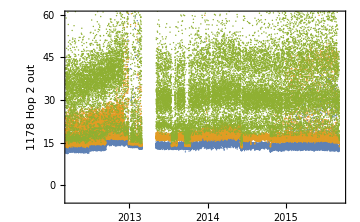
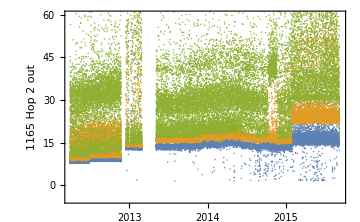
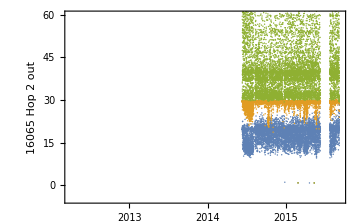
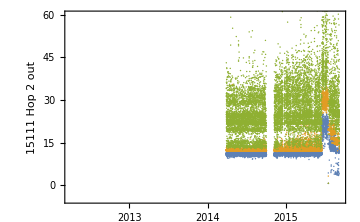
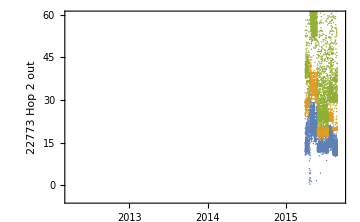
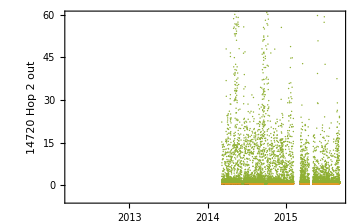
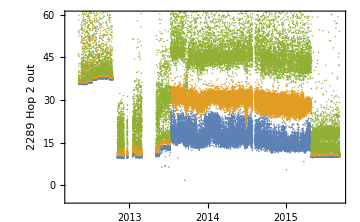
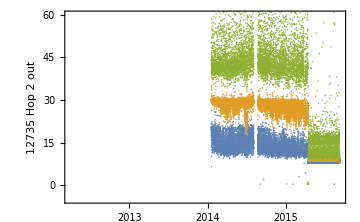

```mathematica
visualizeRTTbyTheHour[probes,{"rtt_5pct", "rtt_med","rtt_95pct"},2, {{2012 ,4,1,1,00,0},DateList[]}]
```